# Complex Integration

### Calculus II

In calculus you learned that
	∫_a^b f(x)dx=∫_t_0^t_1 f(x(t))x'(t)dt
where x was a smooth function satisfying x(t_0)=a and x(t_1)=b.  If t_0=0 and t_1=1 then the RHS integral could be computed as  
	∫_0^1 f(x(t))x'(t)dt=lim_(n->∞) ∑_(k=1)^n f(x(k Δt))x'(k Δt)Δt
with Δt=1/n. The RHS is one possible Riemann sum.  A Right hand sum.

### Complex Analysis: FTC Entire Functions

The integral of f(z) along the contour c(t) in the complex plane from t_0 to t_1 is 
	∫_c f(z)dz=∫_t_0^t_1 f(z(t))z'(t)dt
where the contour c is defined by a function z(t) for t_0≤t≤t_1. If t_0=0 and t_1=1 then the RHS integral could be computed with the Riemann sum  
	∫_0^1 f(z(t))z'(t)dt=lim_(n->∞) ∑_(k=1)^n f(z(k Δt))z'(k Δt)Δt
with Δt=1/n. Amazingly the integral often only depends on the end points z(0) and z(1) of the contour!

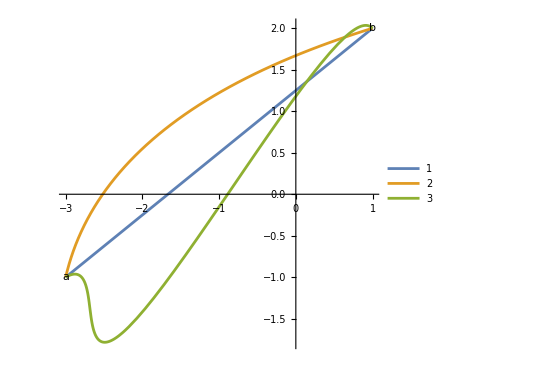

```mathematica
a=-3 - I;b=1+2I;
z1[t_]:=a(1-t) +b t
z2[t_]:= a(1-t) + b t + t(t-1)(3-I)
z3[t_]:= a(1-t) + b t + Sin[4t]Sin[3(t-1)](1+2I)
ParametricPlot[{
ReIm[z1[t]],
ReIm[z2[t]],
ReIm[z3[t]]
},{t,0, 1},
Epilog->{Text["a",ReIm[a]],Text["b",ReIm[b]]},
PlotLegends->Automatic]
```

```mathematica
a=-3 - I;b=1+2I;
z1[t_]:=a(1-t) +b t
z2[t_]:= a(1-t) + b t + t(t-1)(3-I)
z3[t_]:= a(1-t) + b t + Sin[4t]Sin[3(t-1)](1+2I)
f[z_]:= z Sin[z];
n=10000;
Δt=1.0/n;
{Sum[f[z1[k Δt]]z1'[k Δt]Δt,{k,1,n}],
Sum[f[z2[k Δt]]z2'[k Δt]Δt,{k,1,n}],
Sum[f[z3[k Δt]]z3'[k Δt]Δt,{k,1,n}]}
```

{-0.338159+1.80971 ⅈ,-0.337748+1.81041 ⅈ,-0.335954+1.80895 ⅈ}

The analog of the calculus II fundamental theorem
	∫_a^b f(z)dz=F(b)-F(a)
works for entire functions in ℂ.  If f(z)=z sin(z) then F(z)=sin(z)-z cos(z)+const

```mathematica
F[z_]:=Sin[z]-z Cos[z];
N[F[b]-F[a]]
```

-0.33591+1.80778 ⅈ

For an entire function
	∮_c f(z)dz=0
for any closed contour c.

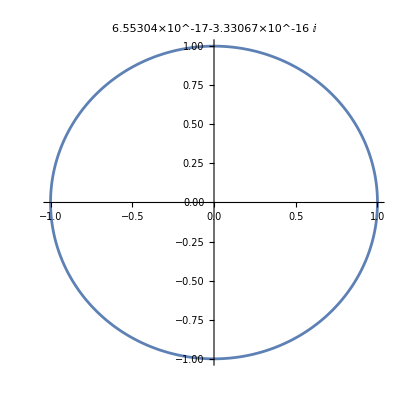

```mathematica
f[z_]:= Cos[Sin[z^2+Cos[z ]]]
z[t_]:= E^(I 2 π t)
n=12; Δt=1.0/n;
ParametricPlot[ReIm[z[t]],{t,0,1},
PlotLabel->Sum[f[z[k Δt]]z'[k Δt] Δt,{k,1,n}]]
```

Lets try a more interesting contour

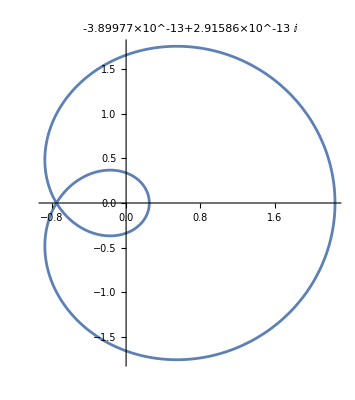

```mathematica
f[z_]:= Cos[Sin[z^2+Cos[z]]]
z[t_]:=( 0.5 +E^(I 2 π t))^2
n=1000; Δt=1.0/n;
ParametricPlot[ReIm[z[t]],{t,0,1},
PlotLabel->Sum[f[z[k Δt]]z'[k Δt] Δt,{k,1,n}]]
```

### Complex Analysis: Functions with Poles

Here is a more interesting contour and a simple function with a pole.  I am going to move the pole around and see how the value changes.  I am also going to change the residue on top of the pole!  Try to guess the value of the contour integral.

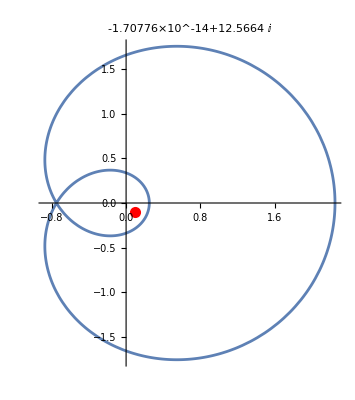

```mathematica
p=0.1-0.1 I;f[z_]:= 1/(z-p)+z Cos[z^2];z[t_]:=( 0.5 +E^(I 2 π t))^2
n=1000; Δt=1.0/n;
ParametricPlot[ReIm[z[t]],{t,0,1},
Epilog->{Red,PointSize[0.02], Point[ReIm[p]]},
PlotLabel->Sum[f[z[k Δt]]z'[k Δt] Δt,{k,1,n}]]
```

For a function 
	f(z)=r/(z-p)+g(z)
with g entire and any closed simple contour c traversed counterclockwise encloses the pole once then
	∮_c f(z)dz=Piecewise[{{0, if p is outside c}, {2π ⅈ r, if p is inside c}}]
The residue r satisfies
	r=lim_(z->p) (z-p)f[z]=lim_(z->p) (z-p)(r/(z-p)+g[z])=lim_(z->p) (r+(z-p)g[z])=r.
This is the simplest form of the residue theorem. 
https://en.wikipedia.org/wiki/Residue_theorem

### Changing Contours: Part One

For a closed contour the integral does not change is we move contour around provided we do not touch a singularity.  Here is an example of a changing contour which has an unchanging integral for any function with no singularities except at “c” the center of the circles.

```mathematica
Clear[p,t]
c=2+I;
p[t_]:= c+((1.2+Cos[2π t])Cos[2π t]+I (2-t)Sin[2π t])
pp[γ_,ϵ_][t_]:=γ p[t]+ (1-γ)(c+ϵ E^(ⅈ 2π t))

Manipulate[
ParametricPlot[{ReIm[p[t]],ReIm[pp[γ,ϵ][t]]},{t,0,1},Epilog->{Red,PointSize[0.02],Point[ReIm[c]]},
PlotLegends->{"p","pp"}],
{{γ,0.9},0,1},
{{ϵ,0.1},0,0.5}]
```

Which contour is easier?

### Changing Contours: Part Two

For a function with a bunch of singularities within a contour we can snap down to small circles round each singularity connected with little bits of two way contours.

```mathematica
{p1,p2,p3}={1+I, 0.2 -0.3 I, -0.8+0.2 I};
TabView[{
"contour"->ParametricPlot[ReIm[2 E^(2π ⅈ t)],{t,0,1},Epilog->{PointSize[0.02],Red,Point[ReIm[{p1,p2,p3}]]}],
"simple contour"->ParametricPlot[ReIm[2 E^(2π ⅈ t)],{t,0,1},
Epilog->{EdgeForm[Green],PointSize[0.02],
Map[Line,ReIm[{{p1,p2},{p1,p3}}]],
{White, Map[Disk[#,0.1]&,ReIm[{p1,p2,p3}]]},
{Red,Point[ReIm[{p1,p2,p3}]]}
}]}
]
```

12

Note: We go along each straight edge twice.
Note: We can head in as close to the singularity as we want.